# Exploring Kyle’s Matrix

Looking at the main matrix.

```mathematica
SetDirectory["C:\\Users\\struther\\Desktop\\2022-23-Classes\\5631\\SampleMatrices\\Week2_Kyle"];
MessyData=ReadList["allTerms.txt",{Character,Number,Character,Number,Character,Real,Character}];
ZeroBaseData=MessyData⟦All,{2,4,6}⟧;
nz=Length[ZeroBaseData];
A=SparseArray[Table[
{i,j,a}=ZeroBaseData⟦k⟧+{1,1,0.0};
{i,j}->a,
{k, nz}]];
MatrixPlot[A]
```

```mathematica
span=Span[3500,4500];
MatrixPlot[A,PlotLegends->Automatic,GridLines->{{m1,m2},None},MeshStyle->Thick]
MatrixPlot[A⟦span,span⟧,PlotLegends->Automatic,Mesh->{{m1,m2},None}]
```

-Graphics-

-Graphics-

-Graphics-

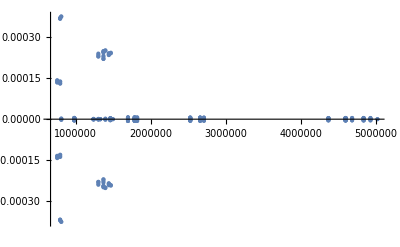

```mathematica
{λs,Vs}=Eigensystem[A,256];
MatrixPlot[Abs[Vs],
PlotLegends->Automatic]
ListPlot[ReIm[λs],PlotRange->All]
```

{4.84915×10^6,0.768498}

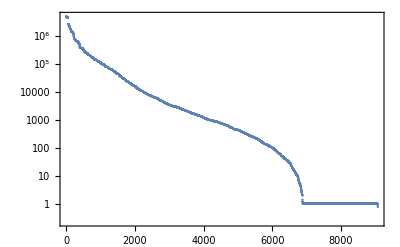

```mathematica
λDia = Eigenvalues[ADia,Method->"Banded"];
{Max[λDia],Min[λDia]}
ListLogPlot[λDia,Frame->True,FrameTicks->Automatic]
```

```mathematica
band=160;
ADia=LowerTriangularize[UpperTriangularize[A,-band],band];
MatrixPlot[A-ADia]
MatrixPlot[A-Aᵀ]
MatrixPlot[ADia-ADiaᵀ, PlotLegends->Automatic]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
?LinearSolve
```

4.42529

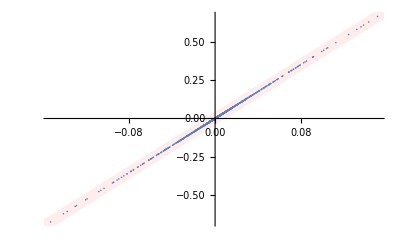

```mathematica
LinSolFun=LinearSolve[ADia,Method->"Banded"];
m=Length[A];
x=RandomReal[{-1,1},m];
Do[x=Chop[Normalize[A.LinSolFun[x]]],300]
Mx=A.LinSolFun[x];
λ=Norm[Mx]
ListPlot[{x,A.LinSolFun[x]}ᵀ,
PlotRange->All,
Prolog->{Directive[LightPink,Thickness[0.02]],Line[{{-1,-λ},{1,λ}}]}]
```

```mathematica
Eigenvalues[{A,ADia},256]
```

-Graphics-

```mathematica
ListLogPlot[Abs[MatrixVals=Sort[ZeroBaseData⟦All,3⟧]]]
```

-Graphics-

```mathematica
π/2.0
```

1.5708

```mathematica
MatrixVals⟦1;;400⟧
MatrixVals⟦-400;;-1⟧
```

{-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-1.59707×10^6,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-798536.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.,-410099.}

{798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,798537.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,820207.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,878139.,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.59707×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,1.75628×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6,3.19415×10^6}

```mathematica
DenseA=Normal[A];
```

```mathematica
{m,m}=Dimensions[A]
{1.0(m^2),(16.0*10^9)}
```

{9075,9075}

{8.23556×10^7,1.6×10^10}

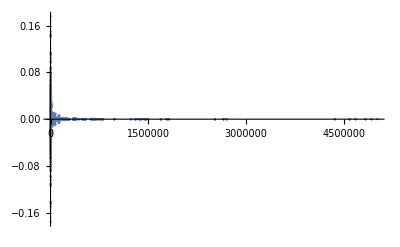

```mathematica
λs=Eigenvalues[DenseA];
ListPlot[ReIm[λs],PlotRange->All]
```

```mathematica
λs⟦1;;12⟧
```

{5.01873×10^6+0. ⅈ,5.01873×10^6+0. ⅈ,4.92551×10^6+0. ⅈ,4.92551×10^6+0. ⅈ,4.92551×10^6+0. ⅈ,4.92551×10^6+0. ⅈ,4.9255×10^6+4.49437×10^-6 ⅈ,4.9255×10^6-4.49437×10^-6 ⅈ,4.9255×10^6+4.25821×10^-6 ⅈ,4.9255×10^6-4.25821×10^-6 ⅈ,4.83402×10^6+4.59817×10^-6 ⅈ,4.83402×10^6-4.59817×10^-6 ⅈ}

```mathematica
NullSpace[ DenseA-(4.834016047741108*^6+ⅈ 4.598172611415327*^-6)IdentityMatrix[m]]
```

```mathematica
2*798536.
```

1.59707×10^6

```mathematica
Eigenvalues[A,12]
```

{5.01873×10^6,5.01873×10^6,4.92551×10^6,4.92551×10^6+1.1781×10^-8 ⅈ,4.92551×10^6-1.1781×10^-8 ⅈ,4.9255×10^6+4.49362×10^-6 ⅈ,4.9255×10^6-4.49362×10^-6 ⅈ,4.9255×10^6+4.2587×10^-6 ⅈ,4.9255×10^6-4.2587×10^-6 ⅈ,4.83402×10^6+4.59825×10^-6 ⅈ,4.83402×10^6-4.59825×10^-6 ⅈ,4.83402×10^6+4.15363×10^-6 ⅈ}

```mathematica
{{"(",0,",",0,")",1,"\n"},{"(",1,",",1,")",1,"\n"},{"(",2,",",2,")",27.6806,"\n"},{"(",2,",",3,")",1.85725,"\n"}}
```

```mathematica
{{"(",0,",",0,")",1},$Failed}
```

I am going to tell the code that parenthesis and commas are “RecordSeparators”, read the rest as “Words” and convert them later.

```mathematica
readStream=OpenRead["allTerms.txt"]

Skip[readStream,Character]
i=Read[readStream,Number]
Skip[readStream,Character]
j=Read[readStream,Number]
Skip[readStream,Character]
a=Read[readStream,Number]
Read[readStream,Record]
Close[readStream]
```

InputStream[…]

0

0

1

(1,1) 1

allTerms.txt

```mathematica
TestDataWords=ReadList["allTerms.txt",Number,3*2,
RecordSeparators->{"\n","(",")","\,"}]
```

ReadList::readn: Invalid real number found when reading from allTerms.txt.

{$Failed}

It is easy to convert to numbers and repartition the entries to get an intermediate form.

```mathematica
TestDataCOOZero=Partition[Map[ToExpression,TestDataWords],3]
```

{{0,0,1},{1,1,1},{2,2,27.6806},{2,3,1.85725},{2,6,-3.46006},{2,7,-0.232158},{2,8,2.70444},{2,9,0.205155},{2,11,-15.3159},{2,12,-0.338054},{2,13,-0.0256445},{2,15,1.91449}}

To convert to a Mathematica Sparse Matrix I need to add one to all of the coordinates!

```mathematica
TestDataMTX=Table[
{i,j,a}=TestDataCOOZero⟦k⟧+{1,1,0.0},
{k,Length[TestDataCOOZero]}]
```

{{1,1,1.},{2,2,1.},{3,3,27.6806},{3,4,1.85725},{3,7,-3.46006},{3,8,-0.232158},{3,9,2.70444},{3,10,0.205155},{3,12,-15.3159},{3,13,-0.338054},{3,14,-0.0256445},{3,16,1.91449}}

To make a Mathematica sparse matrix I just need to make the {i,j}->a list and stick it inside the SparseMatrix constructor. The default makes a matrix just large enough to contain all the specified entries.

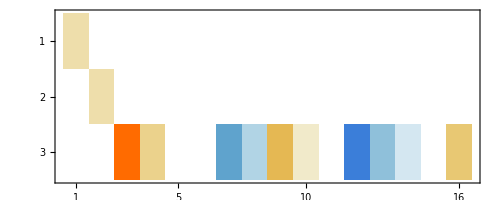

```mathematica
A=SparseArray[Table[
{i,j,a}=TestDataMTX[[k]];
{i,j}->a,
{k,1,Length[TestDataMTX]}]];
MatrixPlot[A]
```

To build the full matrix we need to read (and count) all the entries in the file!

```mathematica
TestData=Partition[ToExpression[ReadList["allTerms.txt",Word,
RecordSeparators->{"\n","(",")",","}]],3];
nz=Length[TestData]
MmaData=ParallelTable[
TestData⟦k⟧+{1,1,0.0},
{k, nz}];
```

1254975

```mathematica
MmaData⟦-1⟧
```

{9075,9064,57.1994}

```mathematica
A=SparseArray[
Table[{i,j,a}=MmaData⟦k⟧;
{i,j}->a,
{k,nz}]]
MatrixPlot[A]
```

SparseArray[<1254975>, {9075, 9075}]

-Graphics-

```mathematica
{m,m}=Dimensions[A];
z=RandomReal[{-1,1},m];
A.z
```

{0.955217,-0.0281679,1,9069,0.515149,-0.754677,638.966+21+0.903208 (-6.+6.50867 e)-0.949484 (-7.+9.99229 e)}
 |  |  |  |

```mathematica
Eigenvalues[A,1]
```

$Aborted

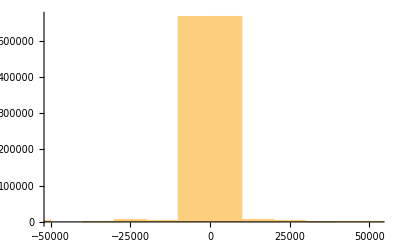

```mathematica
Histogram[MmaData⟦All,3⟧,123]
```